(-26+5 ⅇ^3)/ⅇ^4

1.363191

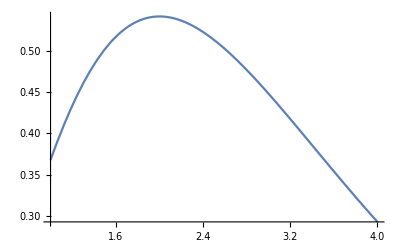

```mathematica
g=x^2 Exp[-x];
A=Integrate[g,{x,1,4}]
N[A,7] (*This provides 7 significant figures*)
Plot[g,{x,1,4}]
```

```mathematica
k=1/A;
f = k*g;
Integrate[f,{x,1,4}]==1
```

True

```mathematica
EV = Integrate[x *f,{x,1,4}]
N[EV,6]
EV//N
```

(2 (-71+8 ⅇ^3))/(-26+5 ⅇ^3)

2.40997

2.40997

```mathematica
Var = Integrate[(x-EV)^2*f,{x,1,4}]
Var//N
```

(3 (420-422 ⅇ^3+23 ⅇ^6))/((26-5 ⅇ^3)^2)

0.66221

(49 π)/4

38.48451

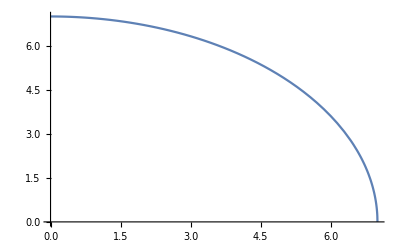

True

2.97089

3.4238

```mathematica
g=Sqrt[49-x^2];
A=Integrate[g,{x,0,7}]
N[A,7] (*This provides 7 significant figures*)
Plot[g,{x,0,7}]
k=1/A;
f = k*g;
Integrate[f,{x,0,7}]==1
EV = Integrate[x *f,{x,0,7}];
EV//N
Var = Integrate[(x-EV)^2*f,{x,0,7}];
Var//N
```

```mathematica
g=Exp[-3x];
bounds={x,0,Infinity};
A=Integrate[g,bounds];
N[A,7] (*This provides 7 significant figures*)
k=1/A;
f=k*g;
Integrate[f,bounds];
EV=Integrate[x*f,bounds];
EV//N (*This is another example of code to obtain a numerical approximation.Typing N[EV] gives the same result.*)
Var=Integrate[(x-EV)^2*f,bounds];
Var//N
```

0.3333333

0.333333

0.111111